```mathematica
ClearAll["Global`*"]
```

```mathematica
(i^•)_sec=B σ Cos[Ω] Sin[i] Sin[Ω];
(Ω^•)_sec=1/2 B Cos[i] (-2+σ+σ Cos[2 Ω])-1;
(ω^•)_sec=Simplify[1/8 B (6-3 σ+σ Cos[2 Ω]-5 Cos[2 i] (-2+σ+σ Cos[2 Ω]))];
(TA^•)_(0 sec)=Simplify[1/8 B (-2+σ+3 (-2+σ) Cos[2 i]-6 σ Cos[2 Ω] Sin[i]^2)+Cos[i]];
(Subscript[M, 0]^•)_sec=Simplify[-1/8 B √(1-e^2) (-2+σ+3 (-2+σ) Cos[2 i]-6 σ Cos[2 Ω] Sin[i]^2)-3 √(1-e^2)  Cos[i]];
(*inam sefr shod*)
```

```mathematica
Solve[(Ω^•)_sec==0,Cos[i]]
```

{{Cos[i]→2/(B (-2+σ+σ Cos[2 Ω]))}}

```mathematica
i=ArcCos[-1/B];
B>1|B<-1;
Ω=π/2;
```

```mathematica
Solve[(ω^•)_sec==0,σ]
```

{{σ→1/2 (3+5 Cos[2 ArcCos[-1/B]])}}

σ=-1+5/B^2
B^2==5/(σ+1)
-1<σ<4

((α-β) (α+β))/(-1+α^2)

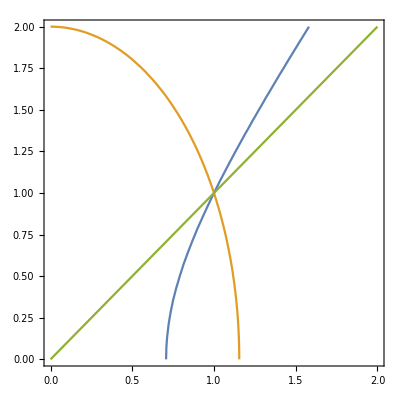

```mathematica
Subscript[ℐ, 𝓍𝓍]=1/5 R^2(β^2+1);
Subscript[ℐ, 𝓎𝓎]=1/5 R^2(1+α^2);
Subscript[ℐ, 𝓏𝓏]=1/5 R^2(β^2+α^2);
σ=FullSimplify[(Subscript[ℐ, 𝓎𝓎]-Subscript[ℐ, 𝓍𝓍])/(Subscript[ℐ, 𝓏𝓏]-Subscript[ℐ, 𝓍𝓍])]
ContourPlot[{2 α^2-β^2==1,3 α^2+β^2==4,α==β},{α,0,2},{β,0,2}]
```

```mathematica
Clear[σ]
$Assumptions=a>0&&R>0;
B=(3n)/(p^2 υ)(Subscript[ℐ, 𝓏𝓏]-Subscript[ℐ, 𝓍𝓍]);
n=√(μ/a^3);
m=(4π)/3 ρ R^3 α β;
μ=G m;

p=a(1-e^2);
B=FullSimplify[(3n(Subscript[ℐ, 𝓏𝓏]-Subscript[ℐ, 𝓍𝓍]))/(2υ p^2)]
```

(√(3 π) (R/a)^(7/2) (-1+α^2) √(G α β ρ))/(5 (-1+e^2)^2 υ)

```mathematica
a=( √(3/125 π G α β ρ(1+σ)) (1-α^2)/υ)^(2/7)(1-e^2)^(-4/7)R;
FullSimplify[B^2==5/(1+σ)]
```

True

```mathematica
(* B>1 for quasi frozen and B^2>5/(1+σ) for frozen *)
a=R;
e=0;
B^2>1
B^2>5/(1+σ)
```

(3 G π α (-1+α^2)^2 β ρ)/(25 υ^2)>1

(3 G π α (-1+α^2)^2 β ρ)/(25 υ^2)>5/(1+σ)

```mathematica
ClearAll["Global`*"]
α=1.5;
β=1;
ρ=1500;
R=1;
G=6.67 10^-11;
e=0.5;
ω=0°;
Ω=90°;
T=100 3600;
υ=N[(2π)/T];
m=4/3 π R^3 ρ α β;
μ=G m;
σ=((α-β) (α+β))/(-1+α^2);
a=( √(3/125 π G α β ρ(1+σ)) Abs[1-α^2]/υ)^(2/7)(1-e^2)^(-4/7)R;
B=(√(3 π) (R/a)^(7/2) (-1+α^2) √(G α β ρ))/(5 (-1+e^2)^2 υ);
i=ArcCos[-1/B];


(*a = 3089;
B=Jx 3 √(μ/a^3)1/(υ 2 a^2(1-e^2));
i=ArcCos[-1/B]*)
θ=17.987073609;


(***************************************** Simulation ******************************************)
rp=(a(1-e^2))/(1+e Cos[θ]){Cos[θ],Sin[θ],0};
vp=√(μ/(a(1-e^2))){-Sin[θ],e+Cos[θ],0};
RΩ=({{Cos[Ω], Sin[Ω], 0}, {-Sin[Ω], Cos[Ω], 0}, {0, 0, 1}});
Ri=({{1, 0, 0}, {0, Cos[i], Sin[i]}, {0, -Sin[i], Cos[i]}});
Rω=({{Cos[ω], Sin[ω], 0}, {-Sin[ω], Cos[ω], 0}, {0, 0, 1}});
Qpqw2gcrf=Transpose[Rω.Ri.RΩ];
r0=Qpqw2gcrf.rp;
v0=Qpqw2gcrf.vp;
r=√(x^2+y^2+z^2);

Subscript[ℐ, 𝓍𝓍]=1/5 R^2(1-α^2)+Subscript[ℐ, 𝓏𝓏];
Subscript[ℐ, 𝓎𝓎]=1/5 R^2(1-β^2)+Subscript[ℐ, 𝓏𝓏];
Subscript[U, 0]=μ/r;
Subscript[U, 2]=-1/2 μ/r^3(2 Subscript[ℐ, 𝓏𝓏]-Subscript[ℐ, 𝓍𝓍]-Subscript[ℐ, 𝓎𝓎])+3/2 μ/r^5(x^2(Subscript[ℐ, 𝓏𝓏]-Subscript[ℐ, 𝓍𝓍])+y^2(Subscript[ℐ, 𝓏𝓏]-Subscript[ℐ, 𝓎𝓎]));
coordinaterotaion=1;
dur=1000000;
Subscript[U, x][x_,y_,z_]=D[(Subscript[U, 0]+Subscript[U, 2]), x];
Subscript[U, y][x_,y_,z_]=D[(Subscript[U, 0]+Subscript[U, 2]), y];
Subscript[U, z][x_,y_,z_]=D[(Subscript[U, 0]+Subscript[U, 2]), z];

{p,q,w}=NDSolveValue[{x''[t]-2υ y'[t]-υ^2 x[t]==Subscript[U, x][x[t],y[t],z[t]],
		y''[t]+2υ x'[t]-υ^2 y[t]==Subscript[U, y][x[t],y[t],z[t]],
		z''[t]==Subscript[U, z][x[t],y[t],z[t]],
		x[0]==r0[[1]],x'[0]==v0[[1]],y[0]==r0[[2]],y'[0]==v0[[2]],z[0]==r0[[3]],z'[0]==v0[[3]]},{x,y,z},{t,dur},MaxSteps->10000000];


orbitgcrf=ParametricPlot3D[{Cos[υ t]p[t]-Sin[υ t]q[t],Sin[υ t]p[t]+Cos[υ t]q[t],w[t]},{t,0,dur}];
orbititrf=ParametricPlot3D[{p[t],q[t],w[t]},{t,0,dur},PlotStyle->Thin];
body=ParametricPlot3D[{ R α Cos[u] Sin[v],R β Sin[u] Sin[v],R Cos[v]},{u,0,2 π},{v,-π,π}];
Show[orbitgcrf,body,PlotRange->All,Boxed->False,Axes->False];
Show[orbititrf,body,PlotRange->All,Boxed->False,Axes->False]
Animate[Show[ParametricPlot3D[{Cos[υ t]p[t]-Sin[υ t]q[t],Sin[υ t]p[t]+Cos[υ t]q[t],w[t]},{t,a,a+65000}],ParametricPlot3D[{Cos[ υ a]α Cos[u] Sin[v]-Sin[υ a]β Sin[u] Sin[v],Sin[υ a]α Cos[u] Sin[v]+Cos[υ a]β Sin[u] Sin[v],Cos[v]},{u,0,2 π},{v,-π,π},PerformanceGoal->"Quality",BoxRatios->1,PlotRange->1],PlotRange->All,Boxed->False,Axes->False],{a,0,dur},AnimationRunning->False]
```

-Graphics3D-

```mathematica
rp=(a(1-e^2))/(1+e Cos[θ]){Cos[θ],Sin[θ],0};
vp=√(μ/(a(1-e^2))){-Sin[θ],e+Cos[θ],0};
RΩ=({{Cos[Ω], Sin[Ω], 0}, {-Sin[Ω], Cos[Ω], 0}, {0, 0, 1}});
Ri=({{1, 0, 0}, {0, Cos[i], Sin[i]}, {0, -Sin[i], Cos[i]}});
Rω=({{Cos[ω], Sin[ω], 0}, {-Sin[ω], Cos[ω], 0}, {0, 0, 1}});
Qpqw2gcrf=Transpose[Rω.Ri.RΩ];
r0=Qpqw2gcrf.rp;
v0=Qpqw2gcrf.vp;
r=√(x^2+y^2+z^2);
Subscript[U, 0]=μ/r;
Subscript[U, 2]=-1/2 μ/r^3(Jx+Jy)+3/2 μ/r^5(x^2 Jx+y^2 Jy);
ω=υ;
coordinaterotaion=0;
dur=1000000;
Subscript[U, x][x_,y_,z_]=D[(Subscript[U, 0]+Subscript[U, 2]), x];
Subscript[U, y][x_,y_,z_]=D[(Subscript[U, 0]+Subscript[U, 2]), y];
Subscript[U, z][x_,y_,z_]=D[(Subscript[U, 0]+Subscript[U, 2]), z];

{p,q,w}=NDSolveValue[{x''[t]==Cos[ω t]Subscript[U, x][Cos[ω t]x[t]+Sin[ω t]y[t],-Sin[ω t]x[t]+Cos[ω t]y[t],z[t]]-Sin[ω t]Subscript[U, y][Cos[ω t]x[t]+Sin[ω t]y[t],-Sin[ω t]x[t]+Cos[ω t]y[t],z[t]],
		y''[t]==Sin[ω t]Subscript[U, x][Cos[ω t]x[t]+Sin[ω t]y[t],-Sin[ω t]x[t]+Cos[ω t]y[t],z[t]]+Cos[ω t]Subscript[U, y][Cos[ω t]x[t]+Sin[ω t]y[t],-Sin[ω t]x[t]+Cos[ω t]y[t],z[t]],
		z''[t]==Subscript[U, z][Cos[ω t]x[t]+Sin[ω t]y[t],-Sin[ω t]x[t]+Cos[ω t]y[t],z[t]],
		x[0]==r0[[1]],x'[0]==v0[[1]],y[0]==r0[[2]],y'[0]==v0[[2]],z[0]==r0[[3]],z'[0]==v0[[3]]},{x,y,z},{t,dur},MaxSteps->10000000];

orbitgcrf=ParametricPlot3D[{p[t],q[t],w[t]},{t,0,dur}];
orbititrf=ParametricPlot3D[{Cos[ω t]p[t]+Sin[ω t]q[t],-Sin[ω t]p[t]+Cos[ω t]q[t],w[t]},{t,0,dur},PlotStyle->Thin];
body=ParametricPlot3D[{α Cos[u] Sin[v],α Subscript[η, b] Sin[u] Sin[v],α η Cos[v]},{u,0,2 π},{v,-π,π}];
Show[orbitgcrf,body];
Show[orbititrf,body,PlotRange->All,Boxed->False,Axes->False]
```

-Graphics3D-

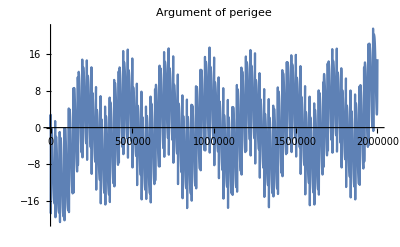

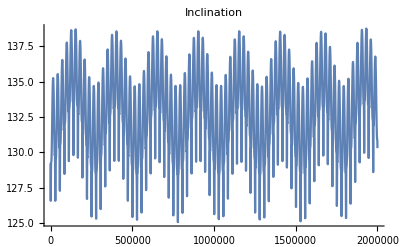

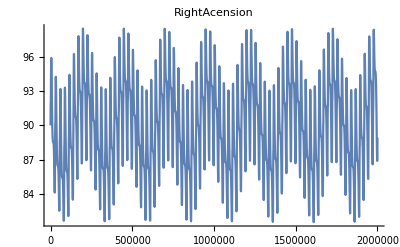

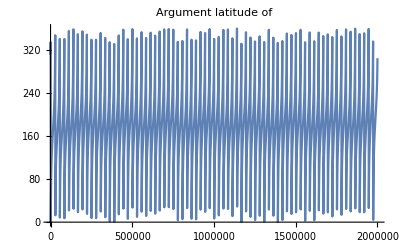

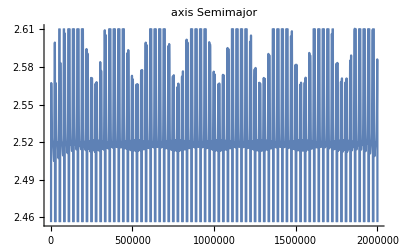

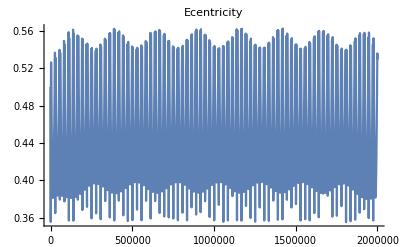

```mathematica
Clear[R]
R[t_]:=If[coordinaterotaion==1,{p[t],q[t],w[t]},{Cos[ω t]p[t]+Sin[ω t]q[t],-Sin[ω t]p[t]+Cos[ω t]q[t],w[t]}]
V[t_]:=R'[t]
d[t_]:=Norm[R[t]]
v[t_]:=Norm[V[t]]
H[t_]:=R[t]×V[t]
h[t_]:=Norm[H[t]]
incle[t_]:=ArcCos[(H[t][[3]])/h[t]]
Na[t_]:={0,0,1}×H[t]
n[t_]:=Norm[Na[t]]
RA[t_]:=If[n[t]≠0,If[Na[t][[2]]≥0,ArcCos[Na[t][[1]]/n[t]],2π-ArcCos[Na[t][[1]]/n[t]]],0];
Ec[t_]:=1/μ((v[t]^2-μ/d[t])R[t]-(R[t].V[t])V[t]);
ec[t_]:=Norm[Ec[t]];
aa[t_]:=h[t]^2/(μ(1-ec[t]^2))
ωp[t_]:=If[Ec[t][[3]]>=0,ArcCos[(Na[t].Ec[t])/(n[t]ec[t])],-ArcCos[(Na[t].Ec[t])/(n[t]ec[t])]]
u[t_]:=If[R[t][[3]]>=0,ArcCos[(Na[t].R[t])/(n[t]d[t])],2π-ArcCos[(Na[t].R[t])/(n[t]d[t])]]
Plot[ωp[t]/°,{t,0,dur},PlotLabel->Argument of perigee]
Plot[incle[t]/°,{t,0,dur},PlotLabel->Inclination]
Plot[RA[t]/°,{t,0,dur},PlotLabel-> RightAcension]
Plot[u[t]/°,{t,0,dur},PlotLabel->Argument of latitude]
Plot[aa[t],{t,0,dur},PlotLabel-> Semimajor axis]
Plot[ec[t],{t,0,dur},PlotLabel->Ecentricity]
```

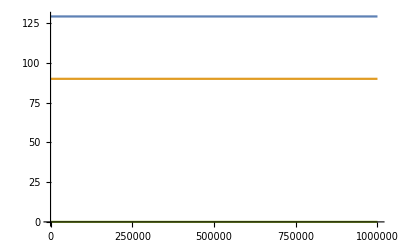

```mathematica
{p,q,w}=NDSolveValue[{x'[t]==B/2 σ υ Sin[x[t]] Sin[2y[t]],y'[t]==1/2 B υ Cos[x[t]] (-2+σ+σ Cos[2 y[t]])-υ,z'[t]==1/8 B υ (6-3 σ+σ Cos[2 y[t]]-5 Cos[2 x[t]] (-2+σ+σ Cos[2 y[t]])),x[0]==i,y[0]==Ω,z[0]==ω},{x,y,z},{t,1000000},MaxSteps->10000000];
Plot[{180/π p[t],180/π q[t],180/π w[t]},{t,0,1000000}]
```